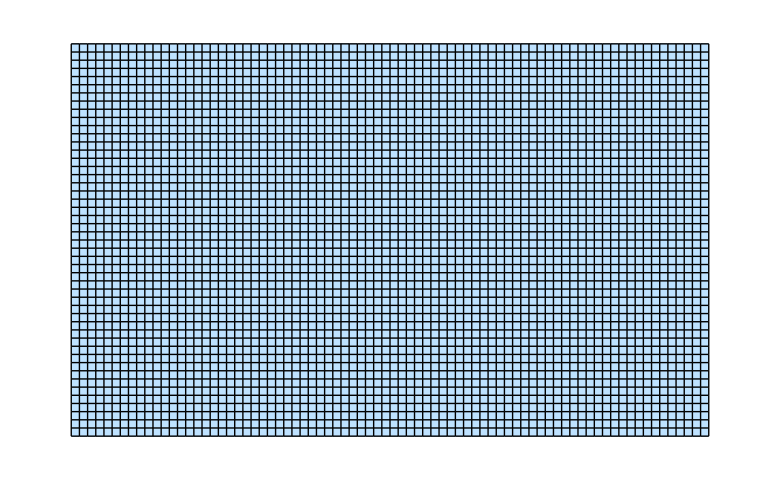

```mathematica
(*Testing to create a GraphicsGrid with visible gridlines*)
noOfColumns=78;
noOfRows=48;
meshFactor=10;
list=ConstantArray["",{48,78}];
Deploy2=Panel[GraphicsGrid[list,ImageSize-> {(noOfColumns*meshFactor),(noOfRows*meshFactor)},Spacings-> {0,0},Background-> RGBColor[.745,.886,1],Alignment-> {Left,Top},Frame->All],ImageSize->{((noOfColumns*meshFactor)+20),((noOfRows*meshFactor)+20)},Background-> RGBColor[.745,.886,1]]
```

```mathematica
(*Testing to make the grid lines like a scale - 9 faint lines, with the 10th dark and thick line*)
noOfColumns=78;
noOfRows=48;
meshFactor=10;
list=ConstantArray["",{48,78}];
Deploy2=Panel[GraphicsGrid[list,ImageSize-> {(noOfColumns*meshFactor),(noOfRows*meshFactor)},Spacings-> {0,0},Background-> RGBColor[.745,.886,1],Alignment-> {Left,Top},Frame->All],ImageSize->{(noOfColumns*meshFactor),(noOfRows*meshFactor)},Background-> RGBColor[.745,.886,1]]
```